# economic analysis

## import data

(1) raw data 

base-case scenario
(2) median
(3) uncertainty
(4) full

stewardship
(5) median
(6) uncertainty
(7) full

switch year
(8) median
(9) uncertainty
(10) full

(11) cbp consumption {SQ, I}
(12) switch year {SQ, I}
(13) mortality {mS, mA, mR}

### preparing directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCeaalls"]]}];
```

### load data

```mathematica
nod=3; (*# of indications*)

(*MODEL OUTPUTS*)
Quiet[dataP=ToExpression[Import["pneumonia output.xlsx","Data"]]; (*pneumonia*)
dataS=ToExpression[Import["bacteremia output.xlsx","Data"]]; (*bacteremia*)
dataU=ToExpression[Import["uti output.xlsx","Data"]];] (*uti*)
```

```mathematica
(*DATA & PARAMETERS*)
mdataP=Import["AMR_Datasheet.xlsx",{"Data","Pneu_model"}]; (*PNEUMONIA*)
mdataP = mdataP[[All,2;;]]; 
years = mdataP[[1]]; (*years of available data*)
tt = Length[years];  (*# years of available data*)
pathogens=mdataP[[15]][[1;;3]]; (*pathogen headers*)
nop = Length[pathogens]; (*# of pathogens*)
cbpP=mdataP[[16]][[-1]]; (*proportion of pneumonia patients prescribed cbps*)
inappP=mdataP[[17]][[1]]; (*inappropriate cbp prescription*)
pathP=Table[mdataP[[i]][[-1]],{i,18,20}]; 
(*proportion of pneumonia for PA, AB, KP*)

edataP=mdataP[[21;;]];(*data for economic and health outcomes*) 
stw = edataP[[1]][[1]]; (*reduction in inappropriate therapy*)
pP=edataP[[13]];  (*prevalence of pneumonia*)

mdataS=Import["AMR_Datasheet.xlsx",{"Data","Bacteremia_model"}]; (*BACTEREMIA*)
mdataS = mdataS[[All,2;;]]; 
cbpS=mdataS[[16]][[-1]]; (*proportion of patients prescribed cbps*)
inappS=mdataS[[17]][[1]]; (*inappropriate cbp prescription*)
pathS=Table[mdataS[[i]][[-1]],{i,18,20}]; 
(*proportion of for PA, AB, KP*)

edataS=mdataS[[21;;]];(*data for economic and health outcomes*)
pS=edataS[[13]]; (*prevalence of bacteremia*)

mdataU=Import["AMR_Datasheet.xlsx",{"Data","UTI_model"}]; (*UTI*)
mdataU = mdataU[[All,2;;]]; 
cbpU=mdataU[[16]][[-1]]; (*proportion of patients prescribed cbps*)
inappU=mdataU[[17]][[1]]; (*inappropriate cbp prescription*)
pathU=Table[mdataU[[i]][[-1]],{i,18,20}]; 
(*proportion of for PA, AB, KP*)

edataU=mdataU[[21;;]];(*data for economic and health outcomes*)
pU=edataU[[13]]; (*prevalence of UTI*)

p={pP,pS,pU}; (*prevalence*)

yvals=Range[2000,2040];
```

## model fit plots & projections

### plot consumption

```mathematica
cbpdatP=Table[Transpose@{Range[2000,2040],dataP[[11]][[i]][[k]][[2;;]]},{i,1,2},{k,1,nop}];
cbpdatS=Table[Transpose@{Range[2000,2040],dataS[[11]][[i]][[k]][[2;;]]},{i,1,2},{k,1,nop}];
cbpdatU=Table[Transpose@{Range[2000,2040],dataU[[11]][[i]][[k]][[2;;]]},{i,1,2},{k,1,nop}];

color={RGBColor[0.9,0.6,0],RGBColor[0.25,0.63,0.13],RGBColor[0.1,0.12,0.7]}; (*orange=PA, green=AB, blue=KB*)
marker={Graphics[{color[[1]],Disk[]}],Graphics[{color[[2]],Rectangle[]}],Graphics[{color[[3]],Circle[]}]};
```

```mathematica
(*a,b,c,d are temporary variables*)
a=Show[Table[ListLinePlot[cbpdatP[[1]][[i]][[15;;]],PlotStyle-> {color[[i]]},PlotLabel->Style["Pneumonia",Italic,16],PlotRange->All,TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],0}],{i,1,nop}],
Table[ListLinePlot[cbpdatP[[1]][[i]][[1;;15]],PlotStyle-> {color[[i]]},PlotMarkers-> {marker[[i]],0.03}],{i,1,nop}]];(*pneumonia*)

b=Show[Table[ListLinePlot[cbpdatS[[1]][[i]][[15;;]],PlotStyle-> {color[[i]]},PlotLabel->Style["Bacteremia",Italic,16],PlotRange->{0,0.4},TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],0}],{i,1,nop}],
Table[ListLinePlot[cbpdatS[[1]][[i]][[1;;15]],PlotMarkers->{marker[[i]],0.03},PlotStyle-> {color[[i]]}],{i,1,nop}]]; (*bacteremia*)

c=Show[Table[ListLinePlot[cbpdatU[[1]][[i]][[15;;]],PlotStyle-> {color[[i]]},PlotLabel->Style["UTI",Italic,16],PlotRange->All,TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],0}],{i,1,nop}],
Table[ListLinePlot[cbpdatU[[1]][[i]][[1;;15]],PlotMarkers->{marker[[i]],0.03},PlotStyle-> {color[[i]]}],{i,1,nop}]]; (*UTI*)

d=Panel[GraphicsColumn[{a,b,c},ImageSize-> 500],{Style["Status Quo","Panel",16,Bold,Background->White],Style[Rotate["Carbapenems (SUs)",90 Degree],"Panel",18,Background->White],Style["","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White];
```

```mathematica
(*a,b,c,d1 are temporary variables*)
a=Show[Table[ListLinePlot[cbpdatP[[2]][[i]][[15;;]],PlotRange-> {0,3},PlotLabel->Style["Pneumonia",Italic,16],TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],0},PlotStyle-> {color[[i]],Dashed}],{i,1,nop}],Table[ListLinePlot[cbpdatP[[2]][[i]][[1;;15]],PlotMarkers->{marker[[i]],0.03},PlotStyle-> {color[[i]]}],{i,1,nop}]];(*pneumonia*)

b=Show[Table[ListLinePlot[cbpdatS[[2]][[i]][[15;;]],PlotRange-> {0,0.4},PlotLabel->Style["Bacteremia",Italic,16],TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],0},PlotStyle-> {color[[i]],Dashed}],{i,1,nop}],Table[ListLinePlot[cbpdatS[[2]][[i]][[1;;15]],PlotMarkers->{marker[[i]],0.03},PlotStyle-> {color[[i]]}],{i,1,nop}]];(*bacteremia*)

c=Show[Table[ListLinePlot[cbpdatU[[2]][[i]][[15;;]],PlotRange-> {0,0.25},PlotLabel->Style["UTI",Italic,16],TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],0},PlotStyle-> {color[[i]],Dashed}],{i,1,nop}],Table[ListLinePlot[cbpdatU[[2]][[i]][[1;;15]],PlotMarkers->{marker[[i]],0.03},PlotStyle-> {color[[i]]}],{i,1,nop}]];(*UTI*)

d1=Panel[GraphicsColumn[{a,b,c},ImageSize-> 500],{Style["Stewardship","Panel",16,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White];
```

```mathematica
(*combine plots into graphics grid, add extras, and export!*)
lg=LineLegend[{color[[1]],color[[2]],color[[3]]},{"P. aeruginosa","A. baumannii","K. pneumoniae"},LabelStyle-> Italic,LegendLayout-> "Row",LegendMarkers->marker,LegendMargins-> 15];

cbpplot=
Legended[Panel[GraphicsRow[{d,d1},-75,AspectRatio-> 2,ImageSize-> 1100],
{Style["Year","Panel",18,Background-> White]},{{Bottom,Center}},
Appearance-> "Frameless",Background-> White],Placed[lg,Below]];

(*Export["cbp.jpeg",cbpplot];*)
```

### plot raw data & uncertainty

```mathematica
ss=1000;

rdatP=Table[dataP[[1]][[2]][[i]][[s]]/dataP[[1]][[1]][[1]][[1]],{i,1,nop},{s,1,ss}];
rdatB=Table[dataS[[1]][[2]][[i]][[s]]/dataS[[1]][[1]][[1]][[1]],{i,1,nop},{s,1,ss}];
rdatU=Table[dataU[[1]][[2]][[i]][[s]]/dataU[[1]][[1]][[1]][[1]],{i,1,nop},{s,1,ss}];
```

```mathematica
dataP1=dataP[[1]][[1]]/. 0.-> 1;
rdatP=Table[dataP[[1]][[2]][[i]][[s]]/dataP1[[i]][[s]],{i,1,nop},{s,1,ss}];

dataB1=dataS[[1]][[1]]/. 0.-> 1;
rdatB=Table[dataS[[1]][[2]][[i]][[s]]/dataB1[[i]][[s]],{i,1,nop},{s,1,ss}];

dataU1=dataU[[1]][[1]]/. 0.-> 1;
rdatU=Table[dataU[[1]][[2]][[i]][[s]]/dataU1[[i]][[s]],{i,1,nop},{s,1,ss}];
```

```mathematica
(*95%*)
p95=Table[
Transpose[rdatP[[i]]][[t]][[Ordering[Transpose[rdatP[[i]]][[t]]]]][[26;;975]],
{i,1,nop},{t,1,tt}]; (*pneumonia*)
pm =Table[Median[Transpose[p95[[i]]]],{i,1,nop}];
pyer1=Table[Median[Transpose[p95[[i]]]]-Transpose[p95[[i]]][[1]],{i,1,nop}];
pyer2=Table[Transpose[p95[[i]]][[-1]]-Median[Transpose[p95[[i]]]],{i,1,nop}];

b95=Table[
Transpose[rdatB[[i]]][[t]][[Ordering[Transpose[rdatB[[i]]][[t]]]]][[26;;975]],
{i,1,nop},{t,1,tt}]; (*bacteremia*)
bm =Table[Median[Transpose[b95[[i]]]],{i,1,nop}];
byer1=Table[Median[Transpose[b95[[i]]]]-Transpose[b95[[i]]][[1]],{i,1,nop}];
byer2=Table[Transpose[b95[[i]]][[-1]]-Median[Transpose[b95[[i]]]],{i,1,nop}];

u95=Table[
Transpose[rdatU[[i]]][[t]][[Ordering[Transpose[rdatU[[i]]][[t]]]]][[26;;975]],
{i,1,nop},{t,1,tt}]; (*UTI*)
um =Table[Median[Transpose[u95[[i]]]],{i,1,nop}];
uyer1=Table[Median[Transpose[u95[[i]]]]-Transpose[u95[[i]]][[1]],{i,1,nop}];
uyer2=Table[Transpose[u95[[i]]][[-1]]-Median[Transpose[u95[[i]]]],{i,1,nop}];
```

```mathematica
errorPlot[plot_,data_,xer_,yer_,label_]:=With[{tr=Transpose@data,arrow=Graphics[{Gray,Thin,Line[{{0,1/2},{0,-1/2}}]}]},Module[{PlusMinus,limits,limitsRescaled,dataRescaled,lines,scale},scale=plot/.{ListPlot->{#&,#&},ListLogPlot->{#&,Log},ListLogLogPlot->{Log,Log},ListLogLinearPlot->{Log,#&}};
PlusMinus[a_,b_]:={a-b[[1]],a+b[[2]]};
limits=MapThread[MapThread[PlusMinus,{#,#2}]&,{tr,{xer,yer}}];
limitsRescaled=MapThread[Compose,{scale,limits}];
dataRescaled=MapThread[Compose,{scale,tr}];
lines=Flatten[MapAt[Reverse,MapThread[{{#2[[1]],#},{#2[[2]],#}}&,{Reverse@dataRescaled,limitsRescaled},2],{2,;;,;;}],1];
Show[plot[data,PlotStyle->{Black,AbsolutePointSize@4},Axes->True,Frame->None,PlotLabel-> Style[label,Italic,16]],Graphics[{Arrowheads[{{-.02,0,arrow},{.02,1,arrow}}],Thin,Gray,Arrow[lines]}],PlotRange->({Min[#],Max[#]}&/@Transpose@Flatten[lines,1])]]]
```

```mathematica
plotDp=ConstantArray[Null,{nod,nop}]; (*data*)
For[k=1,k≤ nop,k++,
plotDp[[k]]=
errorPlot[#,Transpose@{years,pm[[k]]},ConstantArray[{0,0},15],Transpose@{pyer1[[k]],
pyer2[[k]]},pathogens[[k]]]&/@{ListPlot}](*data, xer, yer*)

plotDs=ConstantArray[Null,{nod,nop}]; (*data*)
For[k=1,k≤ nop,k++,
plotDs[[k]]=
errorPlot[#,Transpose@{years,bm[[k]]},ConstantArray[{0,0},15],Transpose@{byer1[[k]],
byer2[[k]]},pathogens[[k]]]&/@{ListPlot}](*data, xer, yer*)

plotDu=ConstantArray[Null,{nod,nop}]; (*data*)
For[k=1,k≤ nop,k++,
plotDu[[k]]=
errorPlot[#,Transpose@{years,um[[k]]},ConstantArray[{0,0},15],Transpose@{uyer1[[k]],
uyer2[[k]]},pathogens[[k]]]&/@{ListPlot}](*data, xer, yer*)


plotD={plotDp,plotDs,plotDu};
```

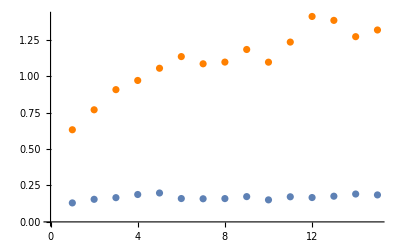

```mathematica
(*test significance of correlation for fit- exclude PA*)
i=1;
Show[
ListPlot[dataP[[11]][[1]][[i]][[2;;16]],PlotStyle-> Orange],ListPlot[pm[[i]]]]
```

```mathematica
a=Table[
SpearmanRankTest[dataP[[11]][[1]][[i]][[2;;16]],pm[[i]]],{i,1,nop}];
b=Table[
SpearmanRankTest[dataS[[11]][[1]][[i]][[2;;16]],bm[[i]]],{i,1,nop}];
c=Table[
SpearmanRankTest[dataU[[11]][[1]][[i]][[2;;16]],um[[i]]],{i,1,nop}];

params= Join[{a},{b},{c}];
headings1=Prepend[params,pathogens];
headings2=MapThread[Prepend,{headings1,{"p","Pneumonia","Bacteremia","UTI_□"}}];
Grid[headings2,Frame-> All]
```

p | Pseudomonas aeruginosa | Acinetobacter baumannii | Klebsiella pneumoniae
Pneumonia | 0.0982941 | 0.0202287 | 3.32487×10^-7
Bacteremia | 0.780755 | 0.00684134 | 0.000103079
UTI_□ | 0.341174 | 0.0435876 | 0.0000257953

```mathematica
Table[
PearsonCorrelationTest[dataP[[11]][[1]][[i]][[2;;16]],pm[[i]]],{i,1,nop}];
Table[
PearsonCorrelationTest[dataS[[11]][[1]][[i]][[2;;16]],bm[[i]]],{i,1,nop}];
Table[
PearsonCorrelationTest[dataU[[11]][[1]][[i]][[2;;16]],um[[i]]],{i,1,nop}];

(*
a=Table[SpearmanRankTest[pm[[i]],dataP[[2]][[i]][[1;;15]]],{i,1,nop}];
b=Table[SpearmanRankTest[bm[[i]],dataS[[2]][[i]][[1;;15]]],{i,1,nop}];
c=Table[SpearmanRankTest[um[[i]],dataU[[2]][[i]][[1;;15]]],{i,1,nop}];

(*create table of fitted values*)
params= Join[{a},{b},{c}];
headings1=Prepend[params,pathogens];
headings2=MapThread[Prepend,{headings1,{"p","Pneumonia","Bacteremia","UTI_□"}}];
Grid[headings2,Frame-> All]*)
```

PearsonCorrelationTest::nortst: At least one of the p-values in {0.010736,0.0718978}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

### no switch year

#### unformatted plots

```mathematica
(*UNCERTAINTY BANDS*)
plotM=ConstantArray[Null,{nod,nop}]; (*model + status quo*)
plotI=ConstantArray[Null,{nod,nop}]; (*intervention- stewardship*)

For[k=1, k≤nop,k++,

plotM[[k]] ={ListLinePlot[Table[Transpose@{yvals,dataP[[3]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,FillingStyle-> GrayLevel[0.92],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals,dataS[[3]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],AxesStyle->Directive[14],PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,FillingStyle-> GrayLevel[0.92],PlotRange-> All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals,dataU[[3]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}}, FillingStyle-> GrayLevel[0.92],AxesOrigin-> {years[[1]],0}]};

plotI[[k]]={ListLinePlot[Table[Transpose@{yvals[[15;;]],dataP[[6]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->
RGBColor[0.3,0.5,0.75,0.25],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[15;;]],dataS[[6]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[15;;]],dataU[[6]][[k]][[j]][[15;;]]},{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75,0.25]},PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}},FillingStyle-> 
RGBColor[0.3,0.5,0.75,0.25],AxesOrigin-> {years[[1]],0}]}]
(*{3 (pneumonia, bacteremia, UTI), 3 (PA, AB, KP)}*)
```

```mathematica
(*BEST FIT*)
plotMb=ConstantArray[Null,{nod,nop}]; (*model + status quo, best fit*)
plotIb=ConstantArray[Null,{nod,nop}]; (*intervention - stewardship, best fit*)

For[k=1, k≤nop,k++,

plotMb[[k]] ={ListLinePlot[Transpose@{yvals,dataP[[2]][[k]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.5],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals,dataS[[2]][[k]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.5],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals,dataU[[2]][[k]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.5],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}]};

plotIb[[k]] ={ListLinePlot[Transpose@{yvals[[15;;]],dataP[[5]][[k]][[15;;]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{RGBColor[0.3,0.5,0.75],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataS[[5]][[k]][[15;;]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{RGBColor[0.3,0.5,0.75],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[15;;]],dataU[[5]][[k]][[15;;]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{RGBColor[0.3,0.5,0.75],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}]}]
(*{3 (pneumonia, bacteremia, UTI), 3 (PA, AB, KP)}*)
```

#### model fit

```mathematica
(*UNCERTAINTY BANDS*)
plotM1=ConstantArray[Null,{nod,nop}]; (*model + status quo*)

For[k=1, k≤nop,k++,
plotM1[[k]] ={ListLinePlot[Table[Transpose@{yvals[[1;;15]],dataP[[3]][[k]][[j]][[1;;15]]},{j,2}],PlotStyle->GrayLevel[0.92],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,FillingStyle-> GrayLevel[0.92],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[1;;15]],dataS[[3]][[k]][[j]][[1;;15]]},{j,2}],PlotStyle->GrayLevel[0.92],AxesStyle->Directive[14],PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,FillingStyle-> GrayLevel[0.92],PlotRange-> All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals[[1;;15]],dataU[[3]][[k]][[j]][[1;;15]]},{j,2}],PlotStyle->GrayLevel[0.92],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}}, FillingStyle-> GrayLevel[0.92],AxesOrigin-> {years[[1]],0}]}];
```

```mathematica
(*BEST FIT*)
plotMb1=ConstantArray[Null,{nod,nop}]; (*model + status quo, best fit*)

For[k=1, k≤nop,k++,
plotMb1[[k]] ={ListLinePlot[Transpose@{yvals[[1;;15]],dataP[[2]][[k]][[1;;15]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.5],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[1;;15]],dataS[[2]][[k]][[1;;15]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.5],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals[[1;;15]],dataU[[2]][[k]][[1;;15]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.5],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}]}];
(*{3 (pneumonia, bacteremia, UTI), 3 (PA, AB, KP)}*)
```

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[{plotM1[[i]][[1]],plotMb1[[i]][[1]],plotD[[1]][[i]][[1]]},Axes-> True,TicksStyle-> FontSize-> 14, PlotRange-> All],{i,1,nop}]; (*pneumonia*)
b=Table[Show[{plotM1[[i]][[2]],plotMb1[[i]][[2]],plotD[[2]][[i]][[1]]},Axes-> True,TicksStyle-> FontSize-> 14,PlotRange-> All],{i,1,nop}]; (*bacteremia*)
c=Table[Show[{plotM1[[i]][[3]],plotMb1[[i]][[3]],plotD[[3]][[i]][[1]]},Axes-> True,TicksStyle-> FontSize-> 14, PlotRange-> All],{i,1,nop}]; (*uti*)d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Bacteremia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add extras, and export!*)
modelfit=Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White]; 

Export["modelfit.jpeg", modelfit];
```

#### all

```mathematica
(*a,b,c,d are temporary variables*)a=Table[Show[{plotM[[i]][[1]],plotMb[[i]][[1]],plotD[[1]][[i]][[1]],plotI[[i]][[1]],plotIb[[i]][[1]]},Axes-> True, TicksStyle-> FontSize-> 14,PlotRange-> All],{i,1,nop}]; (*pneumonia*)
b=Table[Show[{plotM[[i]][[2]],plotMb[[i]][[2]],plotD[[2]][[i]][[1]],plotI[[i]][[2]],plotIb[[i]][[2]]},Axes-> True,TicksStyle-> FontSize-> 14,PlotRange-> All],{i,1,nop}]; (*bacteremia*)
c=Table[Show[{plotM[[i]][[3]],plotMb[[i]][[3]],plotD[[3]][[i]][[1]],plotI[[i]][[3]],plotIb[[i]][[3]]},Axes-> True, TicksStyle-> FontSize-> 14,PlotRange-> All],{i,1,nop}]; (*uti*)d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Bacteremia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add extras, and export!*)
lg=LineLegend[{GrayLevel[0.5],RGBColor[0.3,0.5,0.75]},{"Status quo","Stewardship"},LegendLayout-> "Row",LegendMargins-> 15]; (*legend*)

plot1=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],Placed[lg,Below]] ;

Export["plot1.jpeg", plot1];
```

#### best fit

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[{plotMb[[i]][[1]],plotD[[1]][[i]][[1]],plotIb[[i]][[1]]},Axes-> True,TicksStyle-> FontSize-> 14, PlotRange-> All],{i,1,nop}]; (*pneumonia*)
b=Table[Show[{plotMb[[i]][[2]],plotD[[2]][[i]][[1]],plotIb[[i]][[2]]},Axes-> True,TicksStyle-> FontSize-> 14,PlotRange-> All],{i,1,nop}]; (*bacteremia*)
c=Table[Show[{plotMb[[i]][[3]],plotD[[3]][[i]][[1]],plotIb[[i]][[3]]},Axes-> True,TicksStyle-> FontSize-> 14, PlotRange-> All],{i,1,nop}]; (*uti*)d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Bacteremia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add extras, and export!*)
lg=LineLegend[{GrayLevel[0.5],RGBColor[0.3,0.5,0.75]},{"Status quo","Stewardship"},LegendLayout-> "Row",LegendMargins-> 15]; (*legend*)

plot2=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],Placed[lg,Below]];

Export["bestfit.jpeg", plot2];
```

#### uncertainty

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[{plotM[[i]][[1]],plotD[[1]][[i]][[1]],plotI[[i]][[1]]},Axes-> True, TicksStyle-> FontSize-> 14,PlotRange-> All],{i,1,nop}]; (*pneumonia*)
b=Table[Show[{plotM[[i]][[2]],plotD[[2]][[i]][[1]],plotI[[i]][[2]]},Axes-> True,TicksStyle-> FontSize-> 14,PlotRange-> All],{i,1,nop}]; (*bacteremia*)
c=Table[Show[{plotM[[i]][[3]],plotD[[3]][[i]][[1]],plotI[[i]][[3]]},Axes-> True, TicksStyle-> FontSize-> 14,PlotRange-> All],{i,1,nop}]; (*uti*)d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Bacteremia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add extras, and export!*)
lg=LineLegend[{GrayLevel[0.5],RGBColor[0.3,0.5,0.75]},{"Status quo","Stewardship"},LegendLayout-> "Row",LegendMargins-> 15]; (*legend*)

plot3=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],Placed[lg,Below]]; 

Export["uncertainty.jpeg", plot3];
```

### + switch year

#### unformatted plots

```mathematica
(*{3 (pneumonia, bacteremia, UTI), 3 (PA, AB, KP)}*)

(*UNCERTAINTY BANDS*)
plotSS=ConstantArray[Null,{nod,nop}]; (*model + status quo*)

For[k=1, k≤nop,k++,

plotSS[[k]] ={ListLinePlot[Table[Transpose@{yvals,dataP[[9]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,FillingStyle-> GrayLevel[0.92],AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals,dataS[[9]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],AxesStyle->Directive[14],PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,FillingStyle-> GrayLevel[0.92],PlotRange-> All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[Transpose@{yvals,dataU[[9]][[k]][[j]]},{j,2}],PlotStyle->GrayLevel[0.92],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}}, FillingStyle-> GrayLevel[0.92],AxesOrigin-> {years[[1]],0}]}];
```

```mathematica
(*BEST FIT*)
plotSSb=ConstantArray[Null,{nod,nop}]; (*model + status quo, best fit*)

For[k=1, k≤nop,k++,

plotSSb[[k]] ={ListLinePlot[Transpose@{yvals,dataP[[8]][[k]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.5],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals,dataS[[8]][[k]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.5],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Transpose@{yvals,dataU[[8]][[k]]},FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.5],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}]}];
```

```mathematica
(*SWITCH YEAR*)
cyear=2018; (*current year- start of intervention*)
sySQ={dataP[[12]][[1]],dataS[[12]][[1]],dataU[[12]][[1]]}; (*SQ switch year*)
syI={dataP[[12]][[2]],dataS[[12]][[2]],dataU[[12]][[2]]}; (*intervention switch year*)

ymin={Table[Min[dataP[[8]][[i]],dataS[[5]][[i]],pm[[i]]]*0.95,{i,1,nop}],Table[Min[dataS[[8]][[i]],dataS[[5]][[i]],bm[[i]]]*0.95,{i,1,nop}],Table[Min[dataU[[8]][[i]],dataU[[5]][[i]],um[[i]]]*0.95,{i,1,nop}]}; (*where to put the x axis*)
ymin=Table[If[ymin[[i]][[k]]≤0,0,ymin[[i]][[k]]],{i,1,nod},{k,1,nop}]; (*ensure axis is above 0*)

ymaxb={Table[Max[dataP[[8]][[i]],dataP[[5]][[i]],pm[[i]]]*1.05,{i,1,nop}],Table[Max[dataS[[8]][[i]],dataS[[5]][[i]],bm[[i]]]*1.05,{i,1,nop}],Table[Max[dataU[[8]][[i]],dataU[[5]][[i]],um[[i]]]*1.05,{i,1,nop}]}; (*for PlotRange, best fits*)

ymaxu={Table[Max[dataP[[9]][[i]][[2]],dataP[[6]][[i]][[2]],pm[[i]]]*1.05,{i,1,nop}],Table[Max[dataS[[9]][[i]][[2]],dataS[[6]][[i]][[2]],bm[[i]]],{i,1,nop}],Table[Max[dataU[[9]][[i]][[2]],dataU[[6]][[i]][[2]],um[[i]]]*1.05,{i,1,nop}]}; (*for PlotRange, uncertainties*)

baseSQ=Table[{sySQ[[i]][[k]][[1]],ymin[[i]][[k]]},{i,1,nod},{k,1,nop}];(*for plotting from x axis to switch year*)
baseI=Table[{syI[[i]][[k]][[1]],ymin[[i]][[k]]},{i,1,nod},{k,1,nop}]; (*for plotting from x axis to switch year*)

linestyle=Table[If[sySQ[[i]][[k]][[1]]≥cyear,Null,Dashed],{i,1,nod},{k,1,nop}]; (*dashed lines if SQ switch year occurs prior to current year*)
plotsySQ=Table[Show[ListLinePlot[{baseSQ[[i]][[k]],sySQ[[i]][[k]]},PlotStyle-> {Opacity[0.7],GrayLevel[0.4],Thin,linestyle[[i]][[k]]}],Graphics[{PointSize[Large],Red,Point[sySQ[[i]][[k]]]}]],{i,1,nod},{k,1,nop}];(*switch year under status quo (line+point)*)
plotsyI=Table[Show[ListLinePlot[{baseI[[i]][[k]],syI[[i]][[k]]},PlotStyle-> {Opacity[0.7],GrayLevel[0.4],Thin,linestyle[[i]][[k]]}],Graphics[{PointSize[Large],Darker[Green],Point[syI[[i]][[k]]]}]],{i,1,nod},{k,1,nop}];(*switch year under intervention (line+point)*)
```

#### all

```mathematica
(*a,b,c,d are temporary variables*)a=Table[Show[{plotSS[[i]][[1]],plotSSb[[i]][[1]],plotD[[1]][[i]][[1]],plotI[[i]][[1]],plotIb[[i]][[1]],plotsySQ[[1]][[i]],plotsyI[[1]][[i]]}, TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],ymin[[1]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[1]][[i]],ymaxu[[1]][[i]]}}],{i,1,nop}]; (*pneumonia*)
b=Table[Show[{plotSS[[i]][[2]],plotSSb[[i]][[2]],plotD[[2]][[i]][[1]],plotI[[i]][[2]],plotIb[[i]][[2]],plotsySQ[[2]][[i]],plotsyI[[2]][[i]]},TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],ymin[[2]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[2]][[i]],ymaxu[[2]][[i]]}}],{i,1,nop}];(*bacteremia*)
c=Table[Show[{plotSS[[i]][[3]],plotSSb[[i]][[3]],plotD[[3]][[i]][[1]],plotI[[i]][[3]],plotIb[[i]][[3]],plotsySQ[[3]][[i]],plotsyI[[3]][[i]]}, TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],ymin[[3]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[3]][[i]],ymaxu[[3]][[i]]}}],{i,1,nop}]; (*uti*)

d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Bacteremia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add extras, and export!*)
lg=LineLegend[{GrayLevel[0.5],RGBColor[0.3,0.5,0.75]},{"Status quo","Stewardship"},LegendLayout-> "Row",LegendMargins-> 15]; (*legend*)

plot1f=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],Placed[lg,Below]] ;

Export["plot1f.jpeg", plot1f];
```

#### best fit

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[{plotSSb[[i]][[1]],plotD[[1]][[i]][[1]],plotIb[[i]][[1]],plotsySQ[[1]][[i]],plotsyI[[1]][[i]]},TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],ymin[[1]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[1]][[i]],ymaxb[[1]][[i]]}}],{i,1,nop}];  (*pneumonia*)
b=Table[Show[{plotSSb[[i]][[2]],plotD[[2]][[i]][[1]],plotIb[[i]][[2]],plotsySQ[[2]][[i]],plotsyI[[2]][[i]]},TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],ymin[[2]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[2]][[i]],ymaxb[[2]][[i]]}}],{i,1,nop}];  (*bacteremia*)
c=Table[Show[{plotSSb[[i]][[3]],plotD[[3]][[i]][[1]],plotIb[[i]][[3]],plotsySQ[[3]][[i]],plotsyI[[3]][[i]]},TicksStyle-> FontSize-> 14, AxesOrigin-> {years[[1]],ymin[[3]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[3]][[i]],ymaxb[[3]][[i]]}}],{i,1,nop}]; (*uti*)d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Bacteremia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add extras, and export!*)
lg=LineLegend[{GrayLevel[0.5],RGBColor[0.3,0.5,0.75]},{"Status quo","Stewardship"},LegendLayout-> "Row",LegendMargins-> 15]; (*legend*)

plot2f=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],Placed[lg,Below]];

Export["bestfit f.jpeg", plot2f];
```

#### uncertainty

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[{plotSS[[i]][[1]],plotD[[1]][[i]][[1]],plotI[[i]][[1]]}, TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],ymin[[1]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[1]][[i]],ymaxu[[1]][[i]]}}],{i,1,nop}];  (*pneumonia*)
b=Table[Show[{plotSS[[i]][[2]],plotD[[2]][[i]][[1]],plotI[[i]][[2]]},TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],ymin[[2]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[2]][[i]],ymaxu[[2]][[i]]}}],{i,1,nop}];  (*bacteremia*)
c=Table[Show[{plotSS[[i]][[3]],plotD[[3]][[i]][[1]],plotI[[i]][[3]]}, TicksStyle-> FontSize-> 14,AxesOrigin-> {years[[1]],ymin[[3]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[3]][[i]],ymaxu[[3]][[i]]}}],{i,1,nop}]; (*uti*)d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Bacteremia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add extras, and export!*)
lg=LineLegend[{GrayLevel[0.5],RGBColor[0.3,0.5,0.75]},{"Status quo","Stewardship"},LegendLayout-> "Row",LegendMargins-> 15]; (*legend*)

plot3f=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],Placed[lg,Below]]; 

Export["uncertainty f.jpeg", plot3f];
```

## health outcomes

### mortality

#### base case

```mathematica
(*set up prevalence, 2018-2040*)
pdata=Table[Transpose@{years,p[[i]]},{i,1,nod}]; (*year, prev*)
lm=Table[Normal[LinearModelFit[pdata[[i]],xy,xy]],{i,1,nop}];
plinear[xy_]=lm; (*linear model to project prevalence for future*)
sy=2018; ey=2023; tf=2040; (*start and end years for intervention (sy, ey) and end of projections (tf)*)
yearsI=Range[sy,tf]; (*2018-2040 vector*)
pproj=plinear[yearsI]; (*pneu, sepsis, UTI: projections of prevalence 2018-2040*)

prevP=Table[pproj[[1]]*cbpP*inappP*pathP[[i]],{i,1,nop}]; (*prevalence 2018-2040, cbps, PA, AB, KP*)
prevS=Table[pproj[[2]]*cbpS*inappS*pathS[[i]],{i,1,nop}];
prevU=Table[pproj[[3]]*cbpU*inappU*pathU[[i]],{i,1,nop}];

(*resistance data (full), SY, 2018-2040*)
rSYP=Table[dataP[[10]][[i]][[k]][[Round[sy-years[[1]]+1];;]],{i,1,nop},{k,1,500}]; 
rSYS=Table[dataS[[10]][[i]][[k]][[Round[sy-years[[1]]+1];;]],{i,1,nop},{k,1,500}]; 
rSYU=Table[dataU[[10]][[i]][[k]][[Round[sy-years[[1]]+1];;]],{i,1,nop},{k,1,500}];

(*random sampling 500 from mortality data {P,S,U}*)
mS={RandomSample[dataP[[13]][[1]],500],RandomSample[dataS[[13]][[1]],500],RandomSample[dataU[[13]][[1]],500]};
mA={RandomSample[dataP[[13]][[2]],500],RandomSample[dataS[[13]][[2]],500],RandomSample[dataU[[13]][[2]],500]};
mR={RandomSample[dataP[[13]][[3]],500],RandomSample[dataS[[13]][[3]],500],RandomSample[dataU[[13]][[3]],500]};
```

```mathematica
(*mortality calculations (res + susc): PA, AB, KP*)
mSQres={Table[prevP[[i]]*rSYP[[i]][[k]]*mR[[1]][[k]],{i,1,nop},{k,1,500}],Table[prevS[[i]]*rSYS[[i]][[k]]*mR[[2]][[k]],{i,1,nop},{k,1,500}],Table[prevU[[i]]*rSYU[[i]][[k]]*mR[[3]][[k]],{i,1,nop},{k,1,500}]} ;
(*mortality attributed to resistant {P, S, U}*)

mSQsus={Table[prevP[[i]]*(1-rSYP[[i]][[k]])*mS[[1]][[k]],{i,1,nop},{k,1,500}],Table[prevS[[i]]*(1-rSYS[[i]][[k]])*mS[[2]][[k]],{i,1,nop},{k,1,500}],Table[prevU[[i]]*(1-rSYU[[i]][[k]])*mS[[3]][[k]],{i,1,nop},{k,1,500}]};(*mortality attributed to susceptible {P, S, U}*)


mSQP=mSQres[[1]]+mSQsus[[1]]; (*pneumonia*)
mSQS=mSQres[[2]]+mSQsus[[2]]; (*sepsis*)
mSQU=mSQres[[3]]+mSQsus[[3]];  (*UTI*)
mSQT=Join[mSQP+mSQS+mSQU,{Total[mSQP+mSQS+mSQU]}]; (*TOTAL {PA, AB, KP, TOTAL}*)
```

#### intervention

```mathematica
(*decline in inapp prescription due to stewardship, 2018-2040*)
stwproj=Join[Range[0,stw,stw/(ey-sy+1)],ConstantArray[stw,(tf-ey)]][[2;;]]; (*2017=0, linear increase up to stw by ey, constant until tf*)
```

```mathematica
(*resistance data (best fit), intervention, 2018-2040*)
rIP=Table[dataP[[7]][[i]][[k]][[Round[sy-years[[1]]+1];;]],{i,1,nop},{k,1,500}]; 
rIS=Table[dataS[[7]][[i]][[k]][[Round[sy-years[[1]]+1];;]],{i,1,nop},{k,1,500}]; 
rIU=Table[dataU[[7]][[i]][[k]][[Round[sy-years[[1]]+1];;]],{i,1,nop},{k,1,500}];
```

```mathematica
(*mortality calculations (res_ALT + res_CBP + susc): PA, AB, KP*)
mIres={Table[(prevP[[i]]*rIP[[i]][[k]]*(1-stwproj)*mR[[1]][[k]]),{i,1,nop},{k,1,500}],Table[(prevS[[i]]*rIS[[i]][[k]]*(1-stwproj)*mR[[2]][[k]]),{i,1,nop},{k,1,500}],Table[(prevU[[i]]*rIU[[i]][[k]]*(1-stwproj)*mR[[3]][[k]]),{i,1,nop},{k,1,500}]};
(*mortality attributed to resistant, CBP {P, S, U}*)

mIstw={Table[(prevP[[i]]*rIP[[i]][[k]]*stwproj*mA[[1]][[k]]),{i,1,nop},{k,1,500}],Table[(prevS[[i]]*rIS[[i]][[k]]*stwproj*mA[[2]][[k]]),{i,1,nop},{k,1,500}],Table[(prevU[[i]]*rIU[[i]][[k]]*stwproj*mA[[3]][[k]]),{i,1,nop},{k,1,500}]};
(*mortality attributed to resistant, alt {P, S, U}*)

mIsus={Table[(prevP[[i]]*(1-rIP[[i]][[k]])*mS[[1]][[k]]),{i,1,nop},{k,1,500}],Table[(prevS[[i]]*(1-rIS[[i]][[k]])*mS[[2]][[k]]),{i,1,nop},{k,1,500}], Table[(prevU[[i]]*(1-rIU[[i]][[k]])*mS[[3]][[k]]),{i,1,nop},{k,1,500}]};(*mortality attributed to susceptible {P, S, U}*)
```

```mathematica
mIP=mIres[[1]]+mIstw[[1]]+mIsus[[1]];(*pneumonia*)
mIS=mIres[[2]]+mIstw[[2]]+mIsus[[2]];(*sepsis*)
mIU=mIres[[3]]+mIstw[[3]]+mIsus[[3]];  (*UTI*)
mIT=Join[mIP+mIS+mIU,{Total[mIP+mIS+mIU]}]; (*TOTAL {PA, AB, KP, TOTAL}*)
```

#### median & IQR

```mathematica
(*sum over years*)
mSQPt=Table[Total[Transpose[mSQP[[i]]]],{i,1,nop}];
mSQSt=Table[Total[Transpose[mSQS[[i]]]],{i,1,nop}];
mSQUt=Table[Total[Transpose[mSQU[[i]]]],{i,1,nop}];

mIPt=Table[Total[Transpose[mIP[[i]]]],{i,1,nop}];
mISt=Table[Total[Transpose[mIS[[i]]]],{i,1,nop}];
mIUt=Table[Total[Transpose[mIU[[i]]]],{i,1,nop}];
```

```mathematica
(*Q1,Q2,Q3 
note: can't get Quartiles to work on large #s so scaling it first then scaling back*)
mSQ={Transpose[Table[Quartiles[
mSQPt[[i]]/Mean[mSQPt[[i]]]]*Mean[mSQPt[[i]]],{i,1,nop}] ],
Transpose[Table[Quartiles[
mSQSt[[i]]/Mean[mSQSt[[i]]]]*Mean[mSQSt[[i]]],{i,1,nop}] ],
Transpose[Table[Quartiles[
mSQUt[[i]]/Mean[mSQUt[[i]]]]*Mean[mSQUt[[i]]],{i,1,nop}] ]}; (*diagnosis > pathogen > Q1, Q2, Q3*)

mI={Transpose[Table[Quartiles[
mIPt[[i]]/Mean[mIPt[[i]]]]*Mean[mIPt[[i]]],{i,1,nop}] ],
Transpose[Table[Quartiles[
mISt[[i]]/Mean[mISt[[i]]]]*Mean[mISt[[i]]],{i,1,nop}] ],
Transpose[Table[Quartiles[
mIUt[[i]]/Mean[mIUt[[i]]]]*Mean[mIUt[[i]]],{i,1,nop}] ]}; (*diagnosis > pathogen > Q1, Q2, Q3*)
```